# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 9 - Quantum Monte Carlo

## 9.1 VARIATIONAL QUANTUM MONTE CARLO

### 9.1.1 Prelude: Monte Carlo integration

```mathematica
areaCircle[nTotal_]:=Module[{x,y,nInside=0},
Do[
{x,y}=RandomReal[{-1,1},{2}];
If[x^2+y^2≤1,nInside++];,
{nTotal}];
4*nInside/nTotal
]

areaCircle[1000]//N
```

3.144

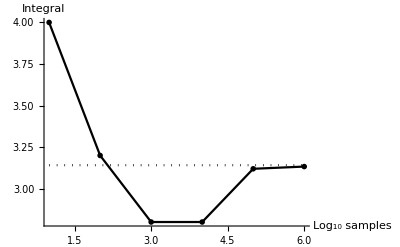

```mathematica
Show[
ListPlot[Table[{n,areaCircle[10n]},{n,1,6}],Joined->True,AxesLabel->{"Log_10 samples","Integral"},PlotRange->All],Plot[Pi,{x,1,6},PlotStyle->{Dotted}] ]
```

```mathematica
psi1DPIB[n_,x_,L_]:=Sqrt[2/L]*Sin[n*Pi*x/L];
L=1.;L*(Sum[(psi1DPIB[1,RandomReal[{0,L}],L])^2,{1000}]/1000)
```

0.959725

### 9.1.2 Case study: Hydrogen atom

```mathematica
trialHAtom[r_,alpha_]:=Exp[-alpha*r] 
trialHAtomFirstDeriv[r_,alpha_]:=-alpha*trialHAtom[r,alpha] 
trialHAtomSecondDeriv[r_,alpha_]:=alpha^2*trialHAtom[r,alpha]
```

```mathematica
HAtomVMC0[alpha_,nSamples_]:=Module[
{numerator=0,denominator=0,r,xyz,Z=1,el=0,mu=1},Do[(*loop over nSamples to evaluate integrals*)
xyz=RandomReal[{-5,5},{3}];
r=Norm[xyz];
numerator+=trialHAtom[r,alpha]*(-1/(2*mu)*
(trialHAtomSecondDeriv[r,alpha]+(2/r)*trialHAtomFirstDeriv[r,alpha])+el*(el+1)*trialHAtom[r,alpha]/(2*mu*r^2)-Z*trialHAtom[r,alpha]/r);denominator+=trialHAtom[r,alpha]^2;
,{nSamples}];
numerator/=nSamples;
denominator/=nSamples;
numerator/denominator
]
```

```mathematica
HAtomVMC0[1.0,5000]
```

-0.5

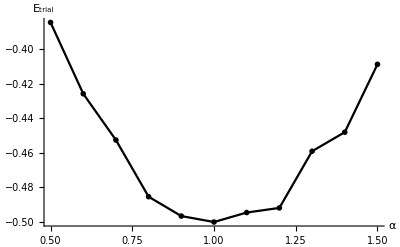

```mathematica
ListPlot[
Table[{alpha,HAtomVMC0[alpha,100000]},{alpha,0.5,1.5,0.1}],
Joined->True,AxesLabel->{"α","E_trial"}]
```

### 9.1.3 Estimating error using block averages

```mathematica
blockAverage[energyFunction_,alpha_,nBlocks_,nSamples_]:=Module[
{energy,energyList={}},
Do[
energy=energyFunction[alpha,nSamples];AppendTo[energyList,energy];
,{nBlocks}];
{Mean[energyList],StandardDeviation[energyList]/Sqrt[nBlocks]}
]
```

```mathematica
blockAverage[HAtomVMC0,0.9,10,100000]
blockAverage[HAtomVMC0,1.0,10,100000]
blockAverage[HAtomVMC0,1.1,10,100000]
```

{-0.496231,0.000923982}

{-0.5,2.26623×10^-17}

{-0.497162,0.00101968}

### 9.1.4 Importance sampling

```mathematica
probHAtom[r_,alpha_]:=(alpha^3/Pi)*trialHAtom[alpha,r]^2
```

```mathematica
KEHAtom[r_,alpha_]:=(alpha/r)-alpha^2/2
```

```mathematica
VHAtom[r_]:=-1/r
```

```mathematica
HAtomVMC1[alpha_,nSamples_]:=Module[
{currentSamples=0,KEaverage=0,Vaverage=0,r,xyz,nTrials=0},While[(currentSamples<nSamples),
xyz=RandomReal[{-5,5},{3}];
r=Norm[xyz];
nTrials++;
If[probHAtom[r,alpha]≥RandomReal[],
currentSamples++;
KEaverage+=KEHAtom[r,alpha];
Vaverage+=VHAtom[r];
];
];
KEaverage/=nSamples;
Vaverage/=nSamples;{KEaverage,Vaverage,(KEaverage+Vaverage),N[nSamples/nTrials]}
]
```

```mathematica
HAtomVMC1[0.9,5000]
HAtomVMC1[1.0,5000]
HAtomVMC1[1.1,5000]
```

{0.40328,-0.898089,-0.494809,0.00101287}

{0.48534,-0.98534,-0.5,0.000984458}

{0.609024,-1.10366,-0.494634,0.00099017}

### 9.1.5 Metropolis sampling

```mathematica
metropolisHAtom[xyz_,stepSize_,alpha_]:=Module[
{r,xyzNEW,rNEW,w,wasAccepted=0},xyzNEW=xyz+stepSize*RandomReal[{-1,1},{3}];r=Norm[xyz];
rNEW=Norm[xyzNEW];w=(trialHAtom[rNEW,alpha]/trialHAtom[r,alpha])^2;If[w≥1,
wasAccepted=1,(*if move to higher-probability position,then accept*)If[RandomReal[]≤w,(*otherwise,accept with some probability*)
wasAccepted=1;(*accept the move*)
];
];
If[wasAccepted==1,
{xyzNEW,rNEW,wasAccepted},(*if accepted,then return new values*)
{xyz,r,wasAccepted} (*if not accepted,then return old values*)
] (*important!:no semicolon on this line so that values get returned*)
];
```

```mathematica
sampleWavefunction[alpha_,nEquil_,nSamples_,stepSize_]:=Module[
{r,xyz,rList={},wasAccepted},
xyz=RandomReal[{-5,5},{3}];
Do[(*equilibrate the system*){xyz,r,wasAccepted}=metropolisHAtom[xyz,stepSize,alpha];
,{nEquil}];
Do[(*collect data*)
{xyz,r,wasAccepted}=metropolisHAtom[xyz,stepSize,alpha];AppendTo[rList,r];
,{nSamples}];
rList (*return the list of sampled positions*)
];
```

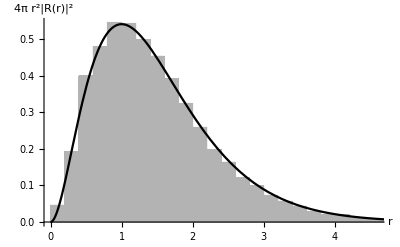

```mathematica
Show[
Histogram[sampleWavefunction[1.0,1000,50000,1.2],Automatic,"PDF",AxesLabel->{"r","4π r^2|R(r)|^2"}],
Plot[4*Pi*r^2*probHAtom[r,1],{r,0,5}] ]
```

```mathematica
HAtomVMC2[alpha_,nEquil_,nSamples_,stepSize_]:=Module[
{KEaverage=0,Vaverage=0,r,xyz,nTrials=0,wasAccepted,nAccepted=0},
xyz=RandomReal[{-5,5},{3}];
Do[(*equilibrate the system*){xyz,r,wasAccepted}=metropolisHAtom[xyz,stepSize,alpha];
,{nEquil}];
Do[(*collect data*)
{xyz,r,wasAccepted}=metropolisHAtom[xyz,stepSize,alpha];nAccepted+=wasAccepted;
KEaverage+=KEHAtom[r,alpha];
Vaverage+=VHAtom[r];
,{nSamples}];
{KEaverage/=nSamples,Vaverage/=nSamples,
(KEaverage+Vaverage),N[nAccepted/(nSamples)]}
];
```

```mathematica
HAtomVMC2[0.9,1000,10000,1.4]
HAtomVMC2[1.0,1000,10000,1.2]
HAtomVMC2[1.1,1000,10000,1.1]
```

{0.428785,-0.926428,-0.497643,0.491}

{0.480312,-0.980312,-0.5,0.5201}

{0.600983,-1.09635,-0.495365,0.511}

## 9.2 DIFFUSION QUANTUM MONTE CARLO

### 9.2.1 Prelude: Classical diffusion

```mathematica
RandomNormal[]:=RandomVariate[ NormalDistribution[] ]
```

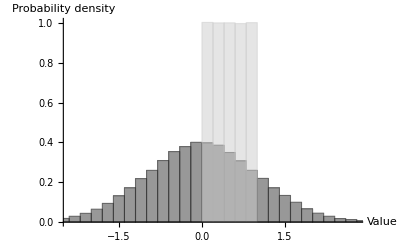

```mathematica
Histogram[
{Table[RandomNormal[],{100000}],Table[RandomReal[],{100000}]}
,Automatic,"PDF",AxesLabel->{"Value","Probability density"} ]
```

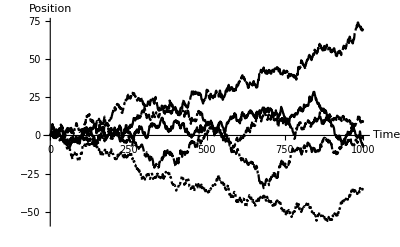

```mathematica
positions={{0},{0},{0},{0},{0}};
Do[(*loop over each particle,i,repeating 1000 times each*)AppendTo[positions[[i]],positions[[i,-1]]+RandomNormal[]];,
{i,1,5},{1000}];

ListPlot[positions,Joined->True,
PlotMarkers->None,AxesLabel->{"Time","Position"}]
```

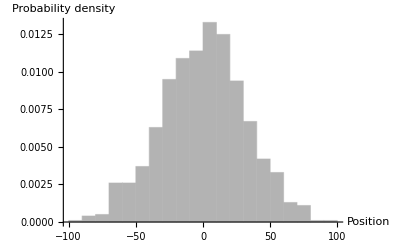

```mathematica
positions=Table[0,{1000}];
Do[ positions[[i]]+=RandomNormal[],{i,1000},{1000}];

Histogram[positions,Automatic,"PDF",
AxesLabel->{"Position","Probability density"}]
```

### 9.2.2 Relationship to the Schrödinger equation

```mathematica
DMCStep[oldXYZ_,dT_,nWalkersTarget_,ER_]:=Module[
{newXYZ,nWalkers=Length[oldXYZ],B,nNewWalkers=0,newCopies},newXYZ=Table[ (*perform random diffusion move*)oldXYZ[[i]]+Sqrt[dT]*{RandomNormal[],RandomNormal[],RandomNormal[]}
,{i,1,nWalkers}];
Do[ (*loop over walkers*)
B=Exp[-(V[newXYZ[[i]]]-ER)*dT]; (*branching probability,Eq.(9.22)*) 
newCopies=Min[IntegerPart[B+RandomReal[]],3]; (*make copies,Eq.(9.23)*)
newXYZ[[i]]=Table[newXYZ[[i]],{newCopies}];
nNewWalkers+=newCopies;
,{i,1,nWalkers}];
(*clean up new walker positions and update ER (Eq.(9.27))*){Partition[Flatten[newXYZ],3],ER+(1-nNewWalkers/nWalkersTarget)/dT}]
```

### 9.2.3 Hydrogen atom

```mathematica
V[position_]:=-1./Norm[position]
```

```mathematica
nWalkersTarget=2000;
walkerXYZ=RandomReal[{-3,3},{nWalkersTarget,3}];initialDistribution=Table[Norm[walkerXYZ[[i]]],{i,1,Length[walkerXYZ]}];ER=0.0;
Do[ {walkerXYZ,ER}=DMCStep[walkerXYZ,0.01,nWalkersTarget,ER],{1000}];finalDistribution=Table[Norm[walkerXYZ[[i]]],{i,1,Length[walkerXYZ]}];
```

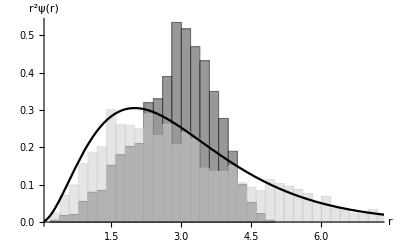

```mathematica
Show[
Histogram[{initialDistribution,finalDistribution},Automatic,"PDF",AxesLabel->{"r","r^2ψ(r)"}],
Plot[1/Sqrt[Pi]*Exp[-r]*r^2,{r,0,9}]]
```

```mathematica
energySamples={};wavefunctionDistribution={};nBlocks=10;Do[(*loop over blocks*)
energySum=0;
Do[ (*loop over walker update timesteps*){walkerXYZ,ER}=DMCStep[walkerXYZ,0.01,nWalkersTarget,ER];
energySum+=ER;
,{500}];
AppendTo[energySamples,energySum/500];
AppendTo[wavefunctionDistribution,Table[Norm[walkerXYZ[[i]]],{i,Length[walkerXYZ]}]];
,{nBlocks}];

{Mean[energySamples],StandardDeviation[energySamples]/Sqrt[nBlocks]}
```

{83.4312,83.8999}

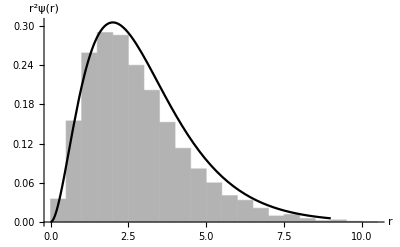

```mathematica
Show[
Histogram[Flatten[wavefunctionDistribution],Automatic,"PDF",AxesLabel->{"r","r^2ψ(r)"}],
Plot[1/Sqrt[Pi]*Exp[-r]*r^2,{r,0,9}]]
```